### Noise and Information in relation to signal detection

#### Setup neural noise [How many neurons, rate of random spikes (numspikes)]

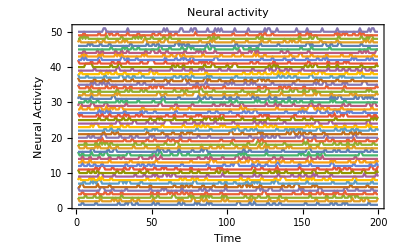

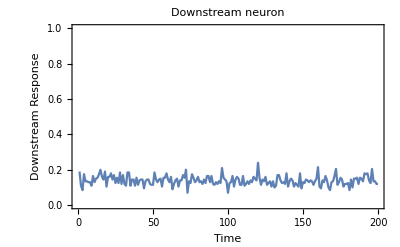

```mathematica
numberOfNeurons=200; (* minimum 2 *)
numspikes=30; (* 30 is a good value, 1/2 of len is coin flips *)

len=200;
t=Range[1,len];

neuronArray=ConstantArray[0,{len,numberOfNeurons}];

Do[spikeIDXs=RandomInteger[{1,len},numspikes];
neuronArray[[spikeIDXs,j]]=1,{j,1,numberOfNeurons}]

avgDownStream=Total[Transpose[neuronArray]];
avgDownStream=avgDownStream/numberOfNeurons;
maxnumtrainstoshow=50;

ListPlot[Table[neuronArray[[All,j]]+j,{j,1,Min[maxnumtrainstoshow,numberOfNeurons]}],PlotRange->{{t[[1]],t[[-1]]},{0.9,Min[maxnumtrainstoshow+1,numberOfNeurons+1]}},Joined->True,PlotStyle->Directive[Opacity[1],Medium],AxesOrigin->{t[[1]],0},Frame->True,FrameLabel->{"Time","Neural Activity"},PlotLabel->"Neural activity"]

(*Plot the downstream neural response*)
ListLinePlot[avgDownStream,PlotRange->{{0,len},{0,1}},AxesOrigin->{t[[1]],0},Frame->True,FrameLabel->{"Time","Downstream Response"},PlotLabel->"Downstream neuron"]
```

We learn from this first part of the simulation is that increasing the number of neurons [INCREASED ENTROPY] surprisingly (or not) decreases the entropy in the downstream neuron.

### Detecting a signal via neural activity

#### An event occurs at the midpoint - set how likely a neuron will respond

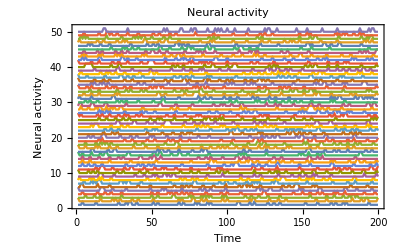

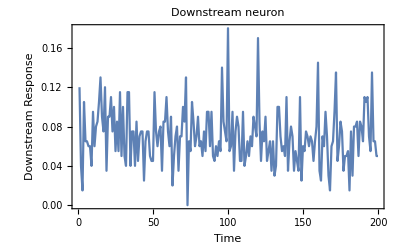

```mathematica
detectionChance=0.20;

neuronDetectorArray=neuronArray;

neuronDetectorArray[[Round[len/2],Flatten[Position[RandomReal[1,numberOfNeurons],x_/;x<=detectionChance]]]]=1;

ListPlot[Table[neuronDetectorArray[[All,j]]+j,{j,1,Min[maxnumtrainstoshow,numberOfNeurons]}],PlotRange->{{t[[1]],t[[-1]]},{0.9,Min[maxnumtrainstoshow+1,numberOfNeurons+1]}},Joined->True,PlotStyle->Directive[Opacity[1],Medium],AxesOrigin->{t[[1]],0},Frame->True,FrameLabel->{"Time","Neural activity"},PlotLabel->"Neural activity"]

avgDownStreamDetector=Total[Transpose[neuronDetectorArray]];
avgDownStreamDetector=avgDownStreamDetector/numberOfNeurons;
ListLinePlot[avgDownStreamDetector - Min[avgDownStreamDetector],PlotRange->{{0,len},{0,Max[avgDownStreamDetector]-Min[avgDownStreamDetector]}},AxesOrigin->{t[[1]],0},Frame->True,FrameLabel->{"Time","Downstream Response"},PlotLabel->"Downstream neuron"]
```

Here we learn that information has a complex relationship with numbers of neurons, noise, and the signal detection threshold.

We also learn that increasing entropy via larger numbers of neurons can lead improved detection of weak signals.